```mathematica
Collect[Series[-2/r+Exp[-(β r)^2](2/r+Subscript[c, 1]+Subscript[c, 2] r+Subscript[c, 3] r^2),{r,0,2}],r,FullSimplify]
```

c_1+r (-2 β^2+c_2)+r^2 (-β^2 c_1+c_3)

```mathematica
Collect[Series[-2/r+Exp[-(β r)^2](2/r-Subscript[U, c]+2 β^2 r-β^2 Subscript[U, c] r^2),{r,0,3}],r,FullSimplify]
```

-r^3 β^4-U_c

```mathematica
f[𝒩_]:=Sum[Subscript[c,n] r^(n-1),{n,0,𝒩-1}]
Collect[Series[-2/r+Exp[-(β r)^2]f[30],{r,0,2}],r,FullSimplify]
Block[{rules},
rules={Subscript[c, 0]->2,Subscript[c, 2]->2 β^2,Subscript[c, 4]->(2 β^4)/2,Subscript[c, 6]->(2 β^6)/6,Subscript[c, 1]->-Subscript[U, c],Subscript[c, 3]->-β^2 Subscript[U, c],Subscript[c, 5]->-(β^4 Subscript[U, c])/2,Subscript[c, 7]->-(β^6 Subscript[U, c])/6};
Collect[Series[-2/r+Exp[-(β r)^2]f[30],{r,0,7}]/.rules,r,FullSimplify]
]
Clear[f];
```

(-2+c_0)/r+c_1+r (-β^2 c_0+c_2)+r^2 (-β^2 c_1+c_3)

r^7 (-β^8/12+c_8)-U_c

```mathematica
f[𝒩_]:=(2/r-Subscript[U, c])Sum[(β r)^(2n)/(n!),{n,0,𝒩-1}]
Collect[Series[-2/r+Exp[-(β r)^2]f[21],{r,0,42}],r,FullSimplify]
Clear[f];
```

-(r^41 β^42)/25545471085854720000-U_c+(r^42 β^42 U_c)/51090942171709440000

```mathematica
Block[{f,g,𝒩=20},
f=(2/r-Subscript[U, c])Sum[((√𝒩)/2 Subscript[U, c] r)^(2n)/(n!),{n,0,𝒩-1}];
g=-2/r+Exp[-((√𝒩)/2 Subscript[U, c] r)^2]f;
Collect[Series[g,{r,0,2𝒩}],r,FullSimplify]
]
```

-U_c-(152587890625 r^39 U_c^40)/1946321606541312+(152587890625 r^40 U_c^41)/3892643213082624

```mathematica
f[𝒩_]:=Sum[Subscript[c,n](r)^(n-1),{n,0,𝒩-1}]-Subscript[U, c] Sum[(β r)^(2n)/(n!),{n,0,𝒩-1}]
Collect[Series[-2/r 𝓀[r]+Exp[-(β r)^2]f[30],{r,0,2}],r,FullSimplify]
Block[{rules},
rules={
Subscript[c, 0]->2𝓀[0],Subscript[c, 2]->(2 β^2)/(2!)(2𝓀[0]+𝓀''[0]/β^2),Subscript[c, 4]->(2 β^4)/(4!) (12𝓀[0]+12 𝓀''[0]/β^2+(Derivative[4][𝓀][0])/β^4),Subscript[c, 6]->(2 β^6)/(6!)(120 𝓀[0]+(180 𝓀''[0])/β^2+(30 Derivative[4][𝓀][0])/β^4+(Derivative[6][𝓀][0])/β^6),
Subscript[c, 1]->(2β)/(1!)(𝓀'[0]/β),Subscript[c, 3]->(2 β^3)/(3!) (6 𝓀'[0]/β+(Derivative[3][𝓀][0])/β^3 ),Subscript[c, 5]->(2 β^5)/(5!)( 60 𝓀'[0]/β+20 (Derivative[3][𝓀][0])/β^3+(Derivative[5][𝓀][0])/β^5),Subscript[c, 7]->(2 β^7)/(7!)((840 𝓀'[0])/β+(420 Derivative[3][𝓀][0])/β^3+(42 Derivative[5][𝓀][0])/β^5+(Derivative[7][𝓀][0])/β^7)
};
Collect[Series[-2/r 𝓀[r]+Exp[-(β r)^2]f[30],{r,0,7}]/.rules,r,FullSimplify]
]
Clear[f];
```

c_1-U_c+(c_0-2 𝓀[0])/r-2 𝓀'[0]+r (-β^2 c_0+c_2-𝓀''[0])+r^2 (-β^2 c_1+c_3-1/3 𝓀^(3)[0])

-U_c+r^7 (c_8+(-56 β^2 (15 β^2 (2 β^4 𝓀[0]+4 β^2 𝓀''[0]+𝓀^(4)[0])+𝓀^(6)[0])-𝓀^(8)[0])/20160)

```mathematica
f[𝒩_]:=2/r Sum[Subscript[c,n](β r)^n/(n!),{n,0,𝒩-1}]-Subscript[U, c] Sum[(β r)^(2m)/(m!),{m,0,Quotient[𝒩,2]}]
Collect[Series[-2/r 𝓀[r]+Exp[-(β r)^2]f[30],{r,0,2}],r,FullSimplify]
Block[{rules},
rules={
Subscript[c, 0]->𝓀[0],Subscript[c, 2]->2𝓀[0]+𝓀''[0]/β^2,Subscript[c, 4]->12𝓀[0]+12 𝓀''[0]/β^2+(Derivative[4][𝓀][0])/β^4,Subscript[c, 6]->120 𝓀[0]+(180 𝓀''[0])/β^2+(30 Derivative[4][𝓀][0])/β^4+(Derivative[6][𝓀][0])/β^6,Subscript[c, 8]->1680 𝓀[0]+(3360 𝓀''[0])/β^2+(840 Derivative[4][𝓀][0])/β^4+(56 Derivative[6][𝓀][0])/β^6+(Derivative[8][𝓀][0])/β^8,
Subscript[c, 1]->𝓀'[0]/β,Subscript[c, 3]->6 𝓀'[0]/β+(Derivative[3][𝓀][0])/β^3,Subscript[c, 5]-> 60 𝓀'[0]/β+20 (Derivative[3][𝓀][0])/β^3+(Derivative[5][𝓀][0])/β^5,Subscript[c, 7]->(840 𝓀'[0])/β+(420 Derivative[3][𝓀][0])/β^3+(42 Derivative[5][𝓀][0])/β^5+(Derivative[7][𝓀][0])/β^7,Subscript[c, 9]->(15120 𝓀'[0])/β+(10080 Derivative[3][𝓀][0])/β^3+(1512 Derivative[5][𝓀][0])/β^5+(72 Derivative[7][𝓀][0])/β^7+(Derivative[9][𝓀][0])/β^9
};
Collect[Series[-2/r 𝓀[r]+Exp[-(β r)^2]f[30],{r,0,9}]/.rules,r,FullSimplify]
]
Clear[f];
```

2 β c_1-U_c+(2 (c_0-𝓀[0]))/r-2 𝓀'[0]+r (β^2 (-2 c_0+c_2)-𝓀''[0])+1/3 r^2 (β^3 (-6 c_1+c_3)-𝓀^(3)[0])

-U_c+(r^9 (β^10 c_10-90 β^2 (28 β^2 (12 β^6 𝓀[0]+30 β^4 𝓀''[0]+10 β^2 𝓀^(4)[0]+𝓀^(6)[0])+𝓀^(8)[0])-𝓀^(10)[0]))/1814400

```mathematica
Block[{exp},
exp[n_]:=Sum[2^(n-i)Gamma[Mod[n,2]+1/2+Quotient[n,2]]/Gamma[Mod[n,2]+1/2+Quotient[i,2]] Binomial[Quotient[n,2],Quotient[i,2]](D[𝓀[𝓇/β],{𝓇,i}]/.𝓇->0),{i,Mod[n,2],n,2}];
Table[exp[n],{n,0,8,2}]//Print;
Table[exp[n],{n,1,9,2}]//Print;
]
```

{𝓀[0],2 𝓀[0]+𝓀''[0]/β^2,12 𝓀[0]+(12 𝓀''[0])/β^2+(𝓀^(4)[0])/β^4,120 𝓀[0]+(180 𝓀''[0])/β^2+(30 𝓀^(4)[0])/β^4+(𝓀^(6)[0])/β^6,1680 𝓀[0]+(3360 𝓀''[0])/β^2+(840 𝓀^(4)[0])/β^4+(56 𝓀^(6)[0])/β^6+(𝓀^(8)[0])/β^8}

{𝓀'[0]/β,(6 𝓀'[0])/β+(𝓀^(3)[0])/β^3,(60 𝓀'[0])/β+(20 𝓀^(3)[0])/β^3+(𝓀^(5)[0])/β^5,(840 𝓀'[0])/β+(420 𝓀^(3)[0])/β^3+(42 𝓀^(5)[0])/β^5+(𝓀^(7)[0])/β^7,(15120 𝓀'[0])/β+(10080 𝓀^(3)[0])/β^3+(1512 𝓀^(5)[0])/β^5+(72 𝓀^(7)[0])/β^7+(𝓀^(9)[0])/β^9}

```mathematica
Block[{f,expr,𝒩=10},
f=2/r Sum[Sum[2^(n-i)Gamma[Mod[n,2]+1/2+Quotient[n,2]]/Gamma[Mod[n,2]+1/2+Quotient[i,2]] Binomial[Quotient[n,2],Quotient[i,2]](D[𝓀[𝓇/β],{𝓇,i}]/.𝓇->0),{i,Mod[n,2],n,2}](β r)^n/(n!),{n,0,𝒩-1}]-Subscript[U, c] Sum[(β r)^(2m)/(m!),{m,0,Quotient[𝒩,2]}];
expr=-2/r 𝓀[r]+Exp[-(β r)^2]f;
Collect[Series[expr,{r,0,𝒩}],r,FullSimplify]
]
```

-U_c+(r^9 (-90 β^2 (28 β^2 (12 β^6 𝓀[0]+30 β^4 𝓀''[0]+10 β^2 𝓀^(4)[0]+𝓀^(6)[0])+𝓀^(8)[0])-𝓀^(10)[0]))/1814400+(r^10 (-3960 β^4 (14 β^2 (6 β^4 𝓀'[0]+5 β^2 𝓀^(3)[0]+𝓀^(5)[0])+𝓀^(7)[0])-110 β^2 𝓀^(9)[0]-𝓀^(11)[0]))/19958400

```mathematica
Block[{f,𝒩=10},
f=2/r Sum[Sum[2^(n-i)Gamma[Mod[n,2]+1/2+Quotient[n,2]]/Gamma[Mod[n,2]+1/2+Quotient[i,2]] Binomial[Quotient[n,2],Quotient[i,2]](D[𝓀[(2𝓀[0])/(β Subscript[U, c] √𝒩)𝓇],{𝓇,i}]/.𝓇->0),{i,Mod[n,2],n,2}]((β Subscript[U, c] √𝒩)/(2𝓀[0])r)^n/(n!),{n,0,𝒩-1}]-Subscript[U, c] Sum[((β Subscript[U, c] √𝒩)/(2𝓀[0]) r)^(2m)/(m!),{m,0,Quotient[𝒩,2]}];
Assuming[{𝓀[0]>0},Collect[Series[-2/r 𝓀[r]+Exp[-((β Subscript[U, c] √𝒩)/(2𝓀[0])r)^2]f,{r,0,𝒩}],r,Together]]
]
```

-U_c+(r^9 (-2953125 β^10 U_c^10-2953125 β^8 U_c^8 𝓀[0] 𝓀''[0]-393750 β^6 U_c^6 𝓀[0]^3 𝓀^(4)[0]-15750 β^4 U_c^4 𝓀[0]^5 𝓀^(6)[0]-225 β^2 U_c^2 𝓀[0]^7 𝓀^(8)[0]-𝓀[0]^9 𝓀^(10)[0]))/(1814400 𝓀[0]^9)+(r^10 (-32484375 β^10 U_c^10 𝓀'[0]-10828125 β^8 U_c^8 𝓀[0]^2 𝓀^(3)[0]-866250 β^6 U_c^6 𝓀[0]^4 𝓀^(5)[0]-24750 β^4 U_c^4 𝓀[0]^6 𝓀^(7)[0]-275 β^2 U_c^2 𝓀[0]^8 𝓀^(9)[0]-𝓀[0]^10 𝓀^(11)[0]))/(19958400 𝓀[0]^10)

```mathematica
Block[{f,𝒩=4},
f=2/r Sum[Sum[2^(n-i)Gamma[Mod[n,2]+1/2+Quotient[n,2]]/Gamma[Mod[n,2]+1/2+Quotient[i,2]] Binomial[Quotient[n,2],Quotient[i,2]](D[𝓀[(2𝓀[0])/(β Subscript[U, c] √𝒩)𝓇],{𝓇,i}]/.𝓇->0),{i,Mod[n,2],n,2}]((β Subscript[U, c] √𝒩)/(2𝓀[0])r)^n/(n!),{n,0,𝒩-1}]-Subscript[U, c] Sum[((β Subscript[U, c] √𝒩)/(2𝓀[0]) r)^(2m)/(m!),{m,0,Quotient[𝒩,2]}];
Assuming[{𝓀[0]>0},Collect[Series[-2/r 𝓀[r]+Exp[-((β Subscript[U, c] √𝒩)/(2𝓀[0])r)^2]f,{r,0,𝒩}],r,Together]]
]
```

-U_c+(r^3 (-12 β^4 U_c^4-12 β^2 U_c^2 𝓀[0] 𝓀''[0]-𝓀[0]^3 𝓀^(4)[0]))/(12 𝓀[0]^3)+(r^4 (-60 β^4 U_c^4 𝓀'[0]-20 β^2 U_c^2 𝓀[0]^2 𝓀^(3)[0]-𝓀[0]^4 𝓀^(5)[0]))/(60 𝓀[0]^4)

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
β,
f,g,
s,eqn,soln,
plt
},
prec=960;
Δ=SetPrecision[.1,prec];

𝒩=10;
Uc=SetPrecision[100.,prec];


rules=SetPrecision[{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
},prec];
rule=rules[[4]];

f=2/r Sum[Sum[2^(n-i)Gamma[Mod[n,2]+1/2+Quotient[n,2]]/Gamma[Mod[n,2]+1/2+Quotient[i,2]] Binomial[Quotient[n,2],Quotient[i,2]](D[𝓀[(2𝓀[0])/(β Uc √𝒩)𝓇],{𝓇,i}]/.𝓇->0),{i,Mod[n,2],n,2}]((β Uc √𝒩)/(2𝓀[0])r)^n/(n!),{n,0,𝒩-1}]-Subscript[U, c] Sum[((β Uc √𝒩)/(2𝓀[0]) r)^(2m)/(m!),{m,0,Quotient[𝒩,2]}];
g=-2/r 𝓀[r]+Exp[-((β Uc √𝒩)/(2𝓀[0])r)^2]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0},{
D[s,{r,𝒩-1}]/.r->0//FullSimplify,
D[s,{r,𝒩}]/.r->0//FullSimplify
}];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r]/.rule;

Block[{x=NSolve[eqn[[1]]==0,β]},Table[N[x[[n,1]][[2]],5],{n,1,Length[x]}]]//Print;
Block[{x=NSolve[eqn[[2]]==0,β]},Table[N[x[[n,1]][[2]],5],{n,1,Length[x]}]]//Print;
(*Block[{x=Solve[eqn==0,β]},Table[x[[n,1]][[2]],{n,1,Length[x]}]]//Chop//Print;
β=Select[Block[{x=Solve[eqn==0,β]},Table[x[[n,1]][[2]],{n,1,Length[x]}]]//Chop,Positive]//Max;
β//Print;*)
]
```

{-0.0096836 ⅈ,0.0096836 ⅈ,-0.013143 ⅈ,0.013143 ⅈ,-0.018886 ⅈ,0.018886 ⅈ,-0.032581 ⅈ,0.032581 ⅈ,-0.090521 ⅈ,0.090521 ⅈ}

{-0.0090705 ⅈ,0.0090705 ⅈ,-0.011956 ⅈ,0.011956 ⅈ,-0.01642 ⅈ,0.01642 ⅈ,-0.025109 ⅈ,0.025109 ⅈ,-0.050549 ⅈ,0.050549 ⅈ}

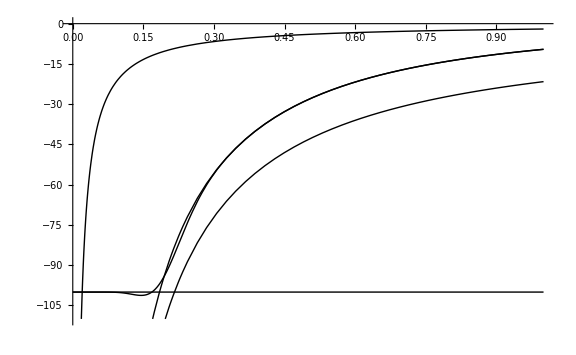
-Graphics-r/r_AUE/E_AU𝒩 = 11

```mathematica
Block[{
prec,Δ,
𝒩,Uc,
𝓀,rules,rule,n,
β,
f,g,
s,eqn,soln,
plt
},
prec=960;
Δ=SetPrecision[.1,prec];

𝒩=11;
Uc=SetPrecision[100.,prec];


rules=SetPrecision[{
{η->11.4,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->10.8,A->1.1750,γ0->0.7572,γ1->0.3223,γ2->2.044},
{η->11.3,A->1.0000,  γ0->0.9500,γ1->0.0000,γ2->2.044},
{η->10.8,A->0.8918,γ0->0.9743,γ1->0.1586,γ2->0.1586}
},prec];
rule=rules[[4]];

f=2/r Sum[Sum[2^(n-i)Gamma[Mod[n,2]+1/2+Quotient[n,2]]/Gamma[Mod[n,2]+1/2+Quotient[i,2]] Binomial[Quotient[n,2],Quotient[i,2]](D[𝓀[(2𝓀[0])/(β Uc √𝒩)𝓇],{𝓇,i}]/.𝓇->0),{i,Mod[n,2],n,2}]((β Uc √𝒩)/(2𝓀[0])r)^n/(n!),{n,0,𝒩-1}]-Uc Sum[((β Uc √𝒩)/(2𝓀[0]) r)^(2m)/(m!),{m,0,Quotient[𝒩,2]}];
g=-2/r 𝓀[r]+Exp[-((β Uc √𝒩)/(2𝓀[0])r)^2]f;

s=Collect[Series[g,{r,0,𝒩}],r,Together];
eqn=Assuming[{Uc>0,𝓀[0]>0},
D[s,{r,𝒩-1}]/.r->0//FullSimplify
];
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r]/.rule;
β=SetPrecision[.8,prec];

Off[General::munfl];
plt=Plot[
{
Style[-Uc,Dashed,Thickness[Medium],Red],Style[-2/r,DotDashed,Thickness[Medium],Darker[Green]],Style[-2/r 𝓀[0],DotDashed,Thickness[Medium],Blue]
,Style[g,Purple],Style[-2/r 𝓀[r],Orange,Thickness[Large]]
}
,{r,0,1}
,WorkingPrecision->prec-10,PerformanceGoal->"Quality",ImageSize->Large
,PlotRange->{(-1-Δ)Uc,0}];
Labeled[plt,{r/Subscript[r, AU],"E/E_AU","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
On[General::munfl];
]
```

```mathematica
Block[{𝓀},
𝓀[r_]=1+A η Exp[-γ0 r]+(1-A)η Exp[-γ1 r]-Exp[-γ2 r];
Table[Derivative[n][𝓀][0],{n,0,4}]
]
```

{(1-A) η+A η,γ2-A γ0 η-(1-A) γ1 η,-γ2^2+A γ0^2 η+(1-A) γ1^2 η,γ2^3-A γ0^3 η-(1-A) γ1^3 η,-γ2^4+A γ0^4 η+(1-A) γ1^4 η}